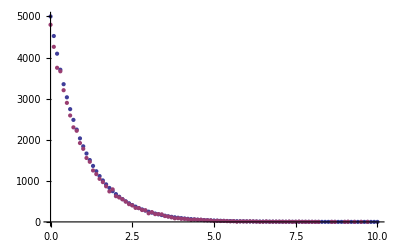

```mathematica
d=10;n=10;nu=50000;ListPlot[{Table[{i/n,Exp[-i/n]*nu/n},{i,0,d n}],Tally[Floor[-Log[1-RandomReal[{0,1},nu]]*n]/n]},PlotRange->All]
```

```mathematica
Integrate[Exp[-i/n],{i,g,g+1}]
```

10 (-1+ⅇ^(1/10)) ⅇ^(1/10 (-1-g))

1.0011

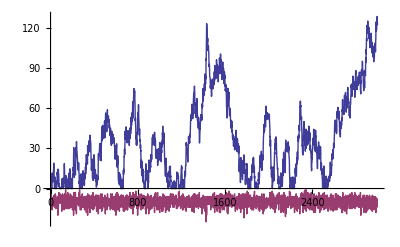

```mathematica
a=1.01;n=10;nu=30000;U={};k=0;j=0;G={};l=0;K=0;
For[i=1,i<nu+1,i++,
k+=-Log[1-RandomReal[]];
If[k>n,
AppendTo[U,i-j];
l+=i-j-a*n;
If[l<0,l=0];
AppendTo[G,l];j=i;k-=n;K+=n;];
];
Sum[U[[i]],{i,Length[U]}]/(K+k)
ListPlot[{G,-U},Joined->True]
```

```mathematica
U
```

{{10.5679},{10.1759},{11.1134},{10.7609},{10.5567},{10.8535},{12.6308},{10.0643},{11.2366},{10.7492}}